```mathematica
M={{0,0,1,0},{0,0,0,1},{Omega^(-2),0,0,-2/Omega},{0,Omega^(-2),2/Omega,0}}
```

{{0,0,1,0},{0,0,0,1},{1/Omega^2,0,0,-2/Omega},{0,1/Omega^2,2/Omega,0}}

```mathematica
MatrixForm[M]
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1/Omega^2 | 0 | 0 | -2/Omega
0 | 1/Omega^2 | 2/Omega | 0)

```mathematica
V[t_] = {w[t],z[t],x[t],y[t]}
```

{w[t],z[t],x[t],y[t]}

```mathematica
system={V[t]==M.V'[t]+{0,0,R,0},x[0]==0,y[0]==0,y'[0]==0,x'[0]==vzero}
```

{{w[t],z[t],x[t],y[t]}=={x'[t],y'[t],R+w'[t]/Omega^2-(2 y'[t])/Omega,(2 x'[t])/Omega+z'[t]/Omega^2},x[0]==0,y[0]==0,y'[0]==0,x'[0]==vzero}

```mathematica
sol=solve=DSolve[system,{w[t],z[t],x[t],y[t]},t]
```

{{w[t]→-1/2 ⅇ^(-ⅈ Omega t) (Omega^2 R t+ⅇ^(2 ⅈ Omega t) Omega^2 R t-vzero-ⅇ^(2 ⅈ Omega t) vzero+ⅈ Omega t vzero-ⅈ ⅇ^(2 ⅈ Omega t) Omega t vzero),x[t]→1/2 ⅇ^(-ⅈ Omega t) (-R+2 ⅇ^(ⅈ Omega t) R-ⅇ^(2 ⅈ Omega t) R-ⅈ Omega R t+ⅈ ⅇ^(2 ⅈ Omega t) Omega R t+t vzero+ⅇ^(2 ⅈ Omega t) t vzero),y[t]→-1/2 ⅇ^(-ⅈ Omega t) (-ⅈ R+ⅈ ⅇ^(2 ⅈ Omega t) R+Omega R t+ⅇ^(2 ⅈ Omega t) Omega R t+ⅈ t vzero-ⅈ ⅇ^(2 ⅈ Omega t) t vzero),z[t]→-1/2 ⅈ ⅇ^(-ⅈ Omega t) (-Omega^2 R t+ⅇ^(2 ⅈ Omega t) Omega^2 R t+vzero-ⅇ^(2 ⅈ Omega t) vzero-ⅈ Omega t vzero-ⅈ ⅇ^(2 ⅈ Omega t) Omega t vzero)}}

```mathematica
xsol[t_]=x[t]/.sol[[1]]
```

1/2 ⅇ^(-ⅈ Omega t) (-R+2 ⅇ^(ⅈ Omega t) R-ⅇ^(2 ⅈ Omega t) R-ⅈ Omega R t+ⅈ ⅇ^(2 ⅈ Omega t) Omega R t+t vzero+ⅇ^(2 ⅈ Omega t) t vzero)

```mathematica
ysol[t_]=y[t]/.sol[[1]]
```

-1/2 ⅇ^(-ⅈ Omega t) (-ⅈ R+ⅈ ⅇ^(2 ⅈ Omega t) R+Omega R t+ⅇ^(2 ⅈ Omega t) Omega R t+ⅈ t vzero-ⅈ ⅇ^(2 ⅈ Omega t) t vzero)

```mathematica
xdet[t_]=Simplify[Re[ExpToTrig[xsol[t]]],Assumptions->t∈Reals&&R∈Reals&&Omega∈Reals&& vzero∈Reals]
```

R+(-R+t vzero) Cos[Omega t]-Omega R t Sin[Omega t]

```mathematica
ydet[t_]=Simplify[Re[ExpToTrig[ysol[t]]],Assumptions->t∈Reals&&R∈Reals&&Omega∈Reals&&vzero∈Reals]
```

-Omega R t Cos[Omega t]+(R-t vzero) Sin[Omega t]

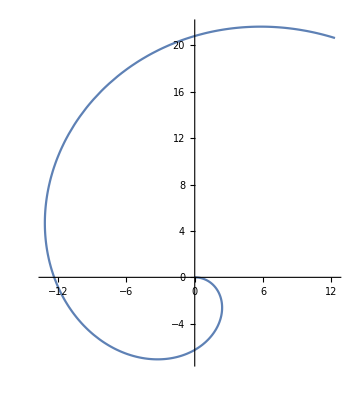

```mathematica
ParametricPlot[{xdet[t],ydet[t]},{t,0,1}]
```

```mathematica
M
```

{{0,0,1,0},{0,0,0,1},{1/Omega^2,0,0,-2/Omega},{0,1/Omega^2,2/Omega,0}}

```mathematica
JordM=JordanDecomposition[M]
```

{{{Omega,-ⅈ Omega^2,Omega,ⅈ Omega^2},{ⅈ Omega,Omega^2,-ⅈ Omega,Omega^2},{-ⅈ,0,ⅈ,0},{1,0,1,0}},{{-ⅈ/Omega,1,0,0},{0,-ⅈ/Omega,0,0},{0,0,ⅈ/Omega,1},{0,0,0,ⅈ/Omega}}}

```mathematica
S=JordM[[1]]
```

{{Omega,-ⅈ Omega^2,Omega,ⅈ Omega^2},{ⅈ Omega,Omega^2,-ⅈ Omega,Omega^2},{-ⅈ,0,ⅈ,0},{1,0,1,0}}

```mathematica
J=JordM[[2]]
```

{{-ⅈ/Omega,1,0,0},{0,-ⅈ/Omega,0,0},{0,0,ⅈ/Omega,1},{0,0,0,ⅈ/Omega}}

```mathematica
IS=Inverse[S]
```

{{0,0,ⅈ/2,1/2},{ⅈ/(2 Omega^2),1/(2 Omega^2),1/(2 Omega),-ⅈ/(2 Omega)},{0,0,-ⅈ/2,1/2},{-ⅈ/(2 Omega^2),1/(2 Omega^2),1/(2 Omega),ⅈ/(2 Omega)}}

```mathematica
MatrixForm[S]
```

(Omega | -ⅈ Omega^2 | Omega | ⅈ Omega^2
ⅈ Omega | Omega^2 | -ⅈ Omega | Omega^2
-ⅈ | 0 | ⅈ | 0
1 | 0 | 1 | 0)

```mathematica
MatrixForm[IS]
```

(0 | 0 | ⅈ/2 | 1/2
ⅈ/(2 Omega^2) | 1/(2 Omega^2) | 1/(2 Omega) | -ⅈ/(2 Omega)
0 | 0 | -ⅈ/2 | 1/2
-ⅈ/(2 Omega^2) | 1/(2 Omega^2) | 1/(2 Omega) | ⅈ/(2 Omega))

```mathematica
MatrixForm[J]
```

(-ⅈ/Omega | 1 | 0 | 0
0 | -ⅈ/Omega | 0 | 0
0 | 0 | ⅈ/Omega | 1
0 | 0 | 0 | ⅈ/Omega)

```mathematica
Rvect={0,0,R,0}
```

{0,0,R,0}

```mathematica
IS.Rvect
```

{(ⅈ R)/2,R/(2 Omega),-(ⅈ R)/2,R/(2 Omega)}

```mathematica
Vprime[t_]={W[t],Z[t],X[t],Y[t]}
```

{W[t],Z[t],X[t],Y[t]}

```mathematica
system2={Vprime[t]==J.Vprime'[t]+IS.Rvect}
```

{{W[t],Z[t],X[t],Y[t]}=={(ⅈ R)/2-(ⅈ W'[t])/Omega+Z'[t],R/(2 Omega)-(ⅈ Z'[t])/Omega,-(ⅈ R)/2+(ⅈ X'[t])/Omega+Y'[t],R/(2 Omega)+(ⅈ Y'[t])/Omega}}

```mathematica
sol2=solve=DSolve[system2,{W[t],Z[t],X[t],Y[t]},t]
```

{{W[t]→(Omega R t)/2+1/2 ⅈ Omega^2 R (1/Omega^2+(ⅈ t)/Omega)+ⅇ^(ⅈ Omega t) C[1]+ⅇ^(ⅈ Omega t) Omega^2 t C[2],Z[t]→R/(2 Omega)+ⅇ^(ⅈ Omega t) C[2],X[t]→(Omega R t)/2-1/2 ⅈ Omega^2 R (1/Omega^2-(ⅈ t)/Omega)+ⅇ^(-ⅈ Omega t) C[3]+ⅇ^(-ⅈ Omega t) Omega^2 t C[4],Y[t]→R/(2 Omega)+ⅇ^(-ⅈ Omega t) C[4]}}

```mathematica
Vprimesol={W[t],Z[t],X[t],Y[t]}/.sol2[[1]]
```

{(Omega R t)/2+1/2 ⅈ Omega^2 R (1/Omega^2+(ⅈ t)/Omega)+ⅇ^(ⅈ Omega t) C[1]+ⅇ^(ⅈ Omega t) Omega^2 t C[2],R/(2 Omega)+ⅇ^(ⅈ Omega t) C[2],(Omega R t)/2-1/2 ⅈ Omega^2 R (1/Omega^2-(ⅈ t)/Omega)+ⅇ^(-ⅈ Omega t) C[3]+ⅇ^(-ⅈ Omega t) Omega^2 t C[4],R/(2 Omega)+ⅇ^(-ⅈ Omega t) C[4]}

```mathematica
xsolgen[t_]=(S.Vprimesol)[[3]]
```

-ⅈ ((Omega R t)/2+1/2 ⅈ Omega^2 R (1/Omega^2+(ⅈ t)/Omega)+ⅇ^(ⅈ Omega t) C[1]+ⅇ^(ⅈ Omega t) Omega^2 t C[2])+ⅈ ((Omega R t)/2-1/2 ⅈ Omega^2 R (1/Omega^2-(ⅈ t)/Omega)+ⅇ^(-ⅈ Omega t) C[3]+ⅇ^(-ⅈ Omega t) Omega^2 t C[4])

```mathematica
ysolgen[t_]=(S.Vprimesol)[[4]]
```

Omega R t-1/2 ⅈ Omega^2 R (1/Omega^2-(ⅈ t)/Omega)+1/2 ⅈ Omega^2 R (1/Omega^2+(ⅈ t)/Omega)+ⅇ^(ⅈ Omega t) C[1]+ⅇ^(ⅈ Omega t) Omega^2 t C[2]+ⅇ^(-ⅈ Omega t) C[3]+ⅇ^(-ⅈ Omega t) Omega^2 t C[4]

```mathematica
solve[{xsolgen[0]==0,ysolgen[0]==0,xsolgen'[0]==vzero,ysolgen'[0]==0}]
```

{{W[t]→(Omega R t)/2+1/2 ⅈ Omega^2 R (1/Omega^2+(ⅈ t)/Omega)+ⅇ^(ⅈ Omega t) C[1]+ⅇ^(ⅈ Omega t) Omega^2 t C[2],Z[t]→R/(2 Omega)+ⅇ^(ⅈ Omega t) C[2],X[t]→(Omega R t)/2-1/2 ⅈ Omega^2 R (1/Omega^2-(ⅈ t)/Omega)+ⅇ^(-ⅈ Omega t) C[3]+ⅇ^(-ⅈ Omega t) Omega^2 t C[4],Y[t]→R/(2 Omega)+ⅇ^(-ⅈ Omega t) C[4]}}[{-ⅈ ((ⅈ R)/2+C[1])+ⅈ (-(ⅈ R)/2+C[3])==0,C[1]+C[3]==0,-ⅈ (ⅈ Omega C[1]+Omega^2 C[2])+ⅈ (-ⅈ Omega C[3]+Omega^2 C[4])==vzero,ⅈ Omega C[1]+Omega^2 C[2]-ⅈ Omega C[3]+Omega^2 C[4]==0}]

```mathematica
xsolgen'[0]==0
```

-ⅈ (ⅈ Omega C[1]+Omega^2 C[2])+ⅈ (-ⅈ Omega C[3]+Omega^2 C[4])==0